```mathematica
Phi[t_]:=-Log[t]^θ
```

```mathematica
D[Phi[t],t]
```

-(θ log^(θ-1)(t))/t

```mathematica
Simplify[D[Phi[t], t]-(θ Phi[t])/(t Log[t])]
```

0

```mathematica
PhiInv[t_]:=Exp[-t^(1/θ)]
```

```mathematica
D[PhiInv[t],t]
```

-(ⅇ^(-t^(1/θ)) t^(1/θ-1))/θ

```mathematica
G[u_,v_]:=PhiInv[Phi[u] + Phi[v]]
```

```mathematica
Simplify[D[D[G[u,v],u],v]]
```

(log^(θ-1)(u) log^(θ-1)(v) ⅇ^(-(-log^θ(u)-log^θ(v))^(1/θ)) (-log^θ(u)-log^θ(v))^(1/θ-2) (θ+(-log^θ(u)-log^θ(v))^(1/θ)-1))/(u v)

```mathematica
Simplify[G[u,v]]
```

ⅇ^(-(-log^θ(u)-log^θ(v))^(1/θ))

```mathematica
Simplify[D[G[u,v],u]]
```

(log^(θ-1)(u) ⅇ^(-(-log^θ(u)-log^θ(v))^(1/θ)) (-log^θ(u)-log^θ(v))^(1/θ-1))/u

```mathematica
Simplify[D[G[u,v], u]-(Log[u]^θ G[u,v] (Phi[u]+Phi[v])^(1/θ))/(u Log[u] (Phi[u]+Phi[v]))]
```

0

```mathematica
Simplify[D[G[u,v], u]-(-D[Phi[u],u] G[u,v] (Phi[u]+Phi[v])^(1/θ))/(θ(Phi[u]+Phi[v]))]
```

0

```mathematica
Simplify[D[G[u,v], u]-D[Phi[u],u] D[PhiInv[q],q]/.q->(Phi[u]+Phi[v])]
```

0

```mathematica
D1Op[w_]:=Simplify[D[G[x,g[v]],x]/.{v->w,x->w},Assumptions->0<w<1]
```

```mathematica
Clear[θ, w, rh]
```

```mathematica
D1Op[w]
```

D::dvar: Multiple derivative specifier {1,3,6,11} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

{(g'(w) ⅇ^(-(-log^θ(g(w))-0^θ)^(1/θ)) log^(θ-1)(g(w)) (-log^θ(g(w))-0^θ)^(1/θ-1))/(g(w)),(g'(w) ⅇ^(-(-log^θ(g(w))-log^θ(3))^(1/θ)) log^(θ-1)(g(w)) (-log^θ(g(w))-log^θ(3))^(1/θ-1))/(g(w)),(g'(w) ⅇ^(-(-log^θ(g(w))-log^θ(6))^(1/θ)) log^(θ-1)(g(w)) (-log^θ(g(w))-log^θ(6))^(1/θ-1))/(g(w)),(g'(w) ⅇ^(-(-log^θ(g(w))-log^θ(11))^(1/θ)) log^(θ-1)(g(w)) (-log^θ(g(w))-log^θ(11))^(1/θ-1))/(g(w))}

```mathematica
g2[w_,rh_,h_]:=Ff[(FsInv[w]-rh)/h]
g[w_]:=Simplify[g2[w,rh,h], Assumptions->0<w<1]
```

```mathematica
Fs[x_]:=CDF[NormalDistribution[2,1],x]
Ff[x_]:=CDF[NormalDistribution[1,1],x]
FsInv[p_]:=InverseCDF[NormalDistribution[2,1],p]
```

```mathematica
h=1; 
θ=10;
1-Integrate[D1Op[w,g[w]], {w,0.0001,.9999}]
```

1-∫_0.0001^0.9999 D1Op(w,1/2 erfc((√2 erfc^-1(2 w)+rh-1)/(√2)))ⅆw

```mathematica
h=1; 
1-Integrate[D1Op[w], {w,0,1}]/.rh->0.5
```

D::dvar: Multiple derivative specifier {1,3,6,11} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

$Aborted

```mathematica
h=1;
rh=-1;
1-NIntegrate[Re[D1Op[w]],{w,0,1}]
```

-1.55143×10^-8

```mathematica
Clear[rh]
```

```mathematica
Re[D1Op[0.5]/.rh->-1]
```

1.02934

```mathematica
Clear[rh]
```

```mathematica
t=Table[{rh,1-NIntegrate[Re[D1Op[w]], {w,0,1}]}, {rh,-2,5,0.2}];
```

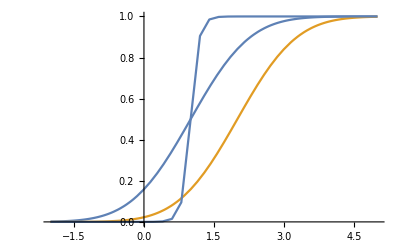

```mathematica
Show[
Plot[{Ff[x],Fs[x]}, {x,-2,5},PlotRange->{0,1}],
ListPlot[t,Joined->True]
]
```